Generalized system

dfdt = a_F(β_F g[f] + (1-β_F) h[r,s] - k[r,f]);
dsdt = a_S (k[r,f] - β_S m[s] - (1 - β_S)h[r,s]);
drdt = a_R(p[r] - l[r,s,f]);

g[f] = Growth function of F
h[r,s] = Recovery function
k[r,f] = Starvation function
m[s] = Mortality function
p[r] = Production of Resource function
l[r,s,f] = Loss of Resource function

a_F = Timescale of F
a_S = Timescale of S
a_R = Timescale of R

β_F = % gain of F due to growth
1-β_F = % gain of F due to recovery

β_S = % loss of S due to mortality
1- β_S = % loss of S due to recovery

Linearization of the generalized system:
Subscripts on the above function denote the partial derative with respect to the subscript
	i.e. 	∂/(∂f)k[r,f] = k_f 
		∂/(∂r)k[r,f] = k_r

```mathematica
ClearAll["Global`*"]
```

### Defining the Full Model

```mathematica
JacM = {{Subscript[a, F]*(Subscript[β, F]*Subscript[g, f]-Subscript[k, f]), Subscript[a, F]*(1-Subscript[β, F])*Subscript[s, h], Subscript[a, F]*((1-Subscript[β, F])*Subscript[s, r]-Subscript[k, r])},
{Subscript[a, H] Subscript[k, f], -Subscript[a, H]*(Subscript[β, H]*Subscript[m, h]+(1-Subscript[β, H])*Subscript[s, h]), Subscript[a, H]*(Subscript[k, r]-(1-Subscript[β, H])*Subscript[s, r])},
{-Subscript[a, R]*Subscript[l, f], -Subscript[a, R]*Subscript[l, h],Subscript[a, R]*(Subscript[p, r] - Subscript[l, r])}};
JacM //MatrixForm
```

(a_F (-k_f+g_f β_F) | a_F s_h (1-β_F) | a_F (-k_r+s_r (1-β_F))
a_H k_f | -a_H (s_h (1-β_H)+m_h β_H) | a_H (k_r-s_r (1-β_H))
-a_R l_f | -a_R l_h | a_R (-l_r+p_r))

We could scale all of the timescales... this may (or may not help interpretation

```mathematica
(*JacM/.{Subscript[a, F]->1, Subscript[a, S]->Subscript[a, S]/Subscript[a, F],Subscript[a, R]->Subscript[a, R]/Subscript[a, F]}*)
```

### Defining the Constrained Generalized Model

```mathematica
JacMSimp = JacM/.{Subscript[l, r]->1,Subscript[l, h]->(1-Subscript[l, f]),Subscript[m, h]->1,Subscript[s, r]->1,Subscript[s, h]->1,Subscript[k, f]->1,Subscript[a, F]->1,Subscript[a, R]->1, Subscript[a, H]->Subscript[a, scaled]}; (*,Subscript[k, r]->1/(1-1/Rstar)*)
JacMSimp//MatrixForm
```

(-1+g_f β_F | 1-β_F | 1-k_r-β_F
a_scaled | -a_scaled | a_scaled (-1+k_r+β_H)
-l_f | -1+l_f | -1+p_r)

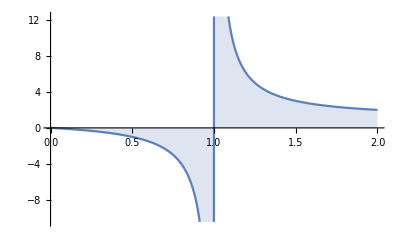

```mathematica
Plot[1/(1-1/Rstar),{Rstar,0,2},Filling->Axis]
```

### Visualization of the Jacobian for the Constrained Generalized Model

```mathematica
Manipulate[
Eig = Eigenvalues[N[JacMSimp]/.{Subscript[g, f]->gf,Subscript[p, r]->pr,Subscript[l, f]->lf,Subscript[k, r]->1/(1-1/Rstar),Subscript[a, scaled]->as,Subscript[β, F]->bf,Subscript[β, S]->bs}];
EigConstellation = Transpose[{Re[Eig],Im[Eig]}];
Show[{
ListPlot[EigConstellation,PlotRange->{{-2,2},{-2,2}},
AspectRatio->1,Frame->True,FrameLabel->{"Real Axis","Imaginary Axis"}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
}],
{{gf,1},0,2},
{{pr,1},0,2},
{{lf,1},0,1},
{{Rstar,0.5},0.001,0.999},
{{as,1},0,2},
{{bf,0.5},0,1},
{{bs,0.5},0,1}]
```

### Stability Analysis of the Constrained Generalized Model

```mathematica
RValues =ParallelTable[
gf = RandomVariate[UniformDistribution[{0,2}]];
pr = RandomVariate[UniformDistribution[{0,2}]];
lf = RandomVariate[UniformDistribution[{0,1}]];
Rstar = RandomVariate[UniformDistribution[{0.001,0.999}]];
as = RandomVariate[UniformDistribution[{0,2}]];
bf = RandomVariate[UniformDistribution[{0,1}]];
bs = RandomVariate[UniformDistribution[{0,1}]];
Eig = Eigenvalues[N[JacMSimp]/.{Subscript[g, f]->gf,Subscript[p, r]->pr,Subscript[l, f]->lf,Subscript[k, r]->1/(1-1/Rstar),Subscript[a, scaled]->as,Subscript[β, F]->bf,Subscript[β, S]->bs}];
MREig = Max[Re[Eig]];
{as,bf,bs,gf,pr,lf,N[1/(1-1/Rstar)],MREig},
{i,0,100000}];
```

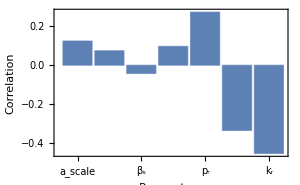

```mathematica
Corr =Table[Correlation[RValues[[All,i]],RValues[[All,8]]],{i,1,7,1}];
CorrChart = BarChart[Corr,ChartLabels->{"a_scale","β_f","β_s","g_f","p_r","l_f","k_r"},Frame->True,ChartStyle->ColorData[97,1],FrameLabel->{"Parameters","Correlation"},ImageSize->300]
```

Observations:

1) As l_fincreases, the consumer population becomes saturated with those in the Full-energetic state, because l_f= F^*/(S^*+F^*). As the consumer population becomes saturated with those in the Full-energetic state, the system becomes STABLE.

2) The elasticity of growth for the Resource is strongly associated with instability
3) The value of the steady state for the resource is strongly associated with instability

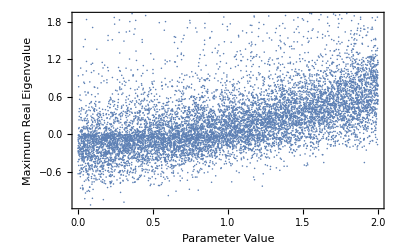

```mathematica
ListPlot[Transpose[{RValues[[All,2]],RValues[[All,8]]}],Frame->True,FrameLabel->{"Parameter Value","Maximum Real Eigenvalue"}]
```

### Correlation between parameters and stability (0, 1) :: this is what we did in our Theoret Ecol paper **THIS IS THE CORRECT ANALYSIS**

```mathematica
JacMSimp//MatrixForm
```

(-1+g_f β_F | 1-β_F | 1-k_r-β_F
a_scaled | -a_scaled | a_scaled (-1+k_r+β_H)
-l_f | -1+l_f | -1+p_r)

```mathematica
StabilityValues =ParallelTable[
gf = RandomVariate[UniformDistribution[{0,2}]];
pr = RandomVariate[UniformDistribution[{-2,2}]];
lf = RandomVariate[UniformDistribution[{0,1}]];
Rstar = RandomVariate[UniformDistribution[{0.001,0.999}]];
as = RandomVariate[UniformDistribution[{0,4}]];
bf = RandomVariate[UniformDistribution[{0,1}]];
bh = RandomVariate[UniformDistribution[{0,1}]];
Eig = Eigenvalues[N[JacMSimp]/.{Subscript[a, scaled]->as,Subscript[β, F]->bf,Subscript[β, H]->bh,Subscript[g, f]->gf,Subscript[p, r]->pr,Subscript[l, f]->lf,Subscript[k, r]->1/(1-1/Rstar)}];
MREig = If[Max[Re[Eig]]<-10^-6,1,0];
{as,bf,bh,gf,pr,lf,N[1/(1-1/Rstar)],MREig},
{i,0,100000}];
```

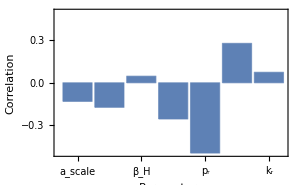

```mathematica
StabilityCorr =Table[
Correlation[StabilityValues[[All,i]],StabilityValues[[All,8]]],
{i,1,7}];
StabilityChart = BarChart[StabilityCorr,ChartLabels->{"a_scale","β_F","β_H","g_f","p_r","l_f","k_r"},PlotRange->{-0.5,0.5},Frame->True,ChartStyle->ColorData[97,1],FrameLabel->{"Parameters","Correlation"},ImageSize->300]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/figs/fig_GenCorr.pdf",StabilityChart]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/figs/fig_GenCorr.pdf

Observations:

Major:
1) There is a strong positive correlation between k_r= F^*/(S^*+F^*) and stability

2) There is a strong negative correlation between growth elasticities and stability

Minor:
3) As a_scale increases, stability tends to decrease... a_scale=a_s/a_r, where a_r= a_f= 1. If a_scale is increasing, the timescale of the Starvers in increasing, meaning that the lifespan is decreasing because Lifespan = 1/timescale. So a quicker turnover of the starving class leads to a greater likelihood of instability... (there is a higher rate of mortality because there are more indivduals entering the starving class.
As the timescale of starvation becomes shorter, the lifespan of the starving class is longer, and the turnover is thus lower... this tends the system towards stability.

4) As the proportional gain of the Full-consumers through growth increases, stability tends to decrease. Likewise, as the proportional gain of the Full-consumers through RECOVERY increases, Stability increases. Higher rates of recovery are good for the system in general. This is possibily similar to the idea that as λ in the specific model increases (increasing the rate of F growth), the system moves towards a TC or Saddle node bifurcation... (not sure which?)

### Analysis of the Full (unconstrained) Generalized Model

There are 15 free parameters, with a Jacobian Matrix:

```mathematica
JacM//MatrixForm
```

(a_F (-k_f+g_f β_F) | a_F h_s (1-β_F) | a_F (-k_r+h_r (1-β_F))
a_S k_f | -a_S (h_s (1-β_S)+m_s β_S) | a_S (k_r-h_r (1-β_S))
-a_R l_f | -a_R l_s | a_R (-l_r+p_r))

```mathematica
RValuesFull =ParallelTable[
af = RandomVariate[UniformDistribution[{0,2}]];
as = RandomVariate[UniformDistribution[{0,2}]];
ar =  RandomVariate[UniformDistribution[{0,2}]];
gf = RandomVariate[UniformDistribution[{0,2}]];
pr = RandomVariate[UniformDistribution[{0,2}]];
lf = RandomVariate[UniformDistribution[{0,2}]];
ls= RandomVariate[UniformDistribution[{0,2}]];
lr= RandomVariate[UniformDistribution[{0,2}]];
ms= RandomVariate[UniformDistribution[{0,2}]];
bf = RandomVariate[UniformDistribution[{0,1}]];
bs = RandomVariate[UniformDistribution[{0,1}]];
kf=RandomVariate[UniformDistribution[{0,2}]];
kr=RandomVariate[UniformDistribution[{-2,2}]];
hs=RandomVariate[UniformDistribution[{0,2}]];
hr=RandomVariate[UniformDistribution[{0,2}]];
Eig = Eigenvalues[N[JacM]/.{
Subscript[a, F]->af,
Subscript[a, S]->as,
Subscript[a, R]->ar,
Subscript[g, f]->gf,
Subscript[p, r]->pr,
Subscript[l, f]->lf,
Subscript[l, s]->ls,
Subscript[l, r]->lr,
Subscript[m, s]->ms,
Subscript[β, F]->bf,
Subscript[β, S]->bs,
Subscript[k, f] -> kf,
Subscript[k, r] -> kr,
Subscript[h, s]-> hs,
Subscript[h, r] -> hr
}];
MREig =  If[Max[Re[Eig]]<-10^-6,1,0];
{af,as,ar,bf,bs,gf,pr,lf,ls,lr,ms, kf, kr, hs, hr,MREig},
{i,0,1000000,1}];
```

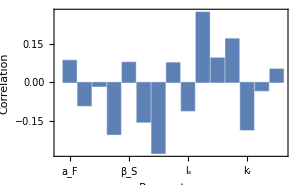

```mathematica
CorrFull =Table[Correlation[RValuesFull[[All,i]],RValuesFull[[All,16]]],{i,1,15,1}];
CorrChartFull = BarChart[CorrFull,ChartLabels->{"a_F","a_S","a_R","β_F","β_S","g_f","p_r","l_f","l_s","l_r","m_s","k_f", "k_r", "h_s", "h_r"},Frame->True,ChartStyle->ColorData[97,1],FrameLabel->{"Parameters","Correlation"},ImageSize->300]
```

```mathematica
StabilityValues
```

{{3.8366,0.226926,0.133439,1.33465,1.8447,0.124338,-0.915999,0},999,{3.05435,0.790639,0.0289534,0.534102,19,0.326307,-3.84395,0}}
 |  |  |  |